## dt = 1 # Time step # PID parameters TARGET_TEMP1 = 44.0 # motor temperature in Celsius pv1 = 0 # Initial process variable kp1 = 5.0 # Proportional gain ki1 = 0.001 # Integral gain kd1 = 0.0 # Derivative gain previous_error1 = 10 integral1 = 0 # TARGET_TEMP2 = -15.0 # motor temperature in Celsius pv2 = 0 # Initial process variable kp2 = 5.0 # Proportional gain ki2 = 0.001 # Integral gain kd2 = 0.0 # Derivative gain previous_error2 = 10 integral2 = 0

```mathematica
a=Import["~/PID-M_2026-05-24_H18_M43_S45/PID-M_2026-05-24_H18_M43_S45.csv"];
```

```mathematica
a[[1]]
```

{2026 May 24 18:43:46.651,1.04,22.5,22.5,0}

```mathematica
a[[Length[a]]]
```

{2026 May 24 20:09:28.228,5142.62,44.1875,10.625,0}

```mathematica
Length[a]
```

4601

```mathematica
b1=Table[{a[[i,2]],a[[i,3]]},{i,Length[a]}];
```

```mathematica
b2=Table[{a[[i,2]],a[[i,4]]},{i,Length[a]}];
```

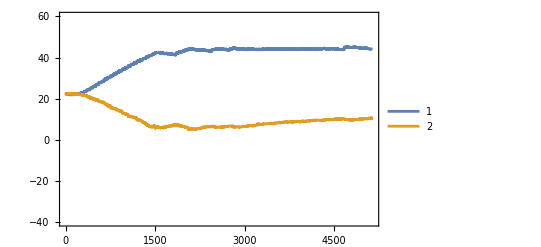

```mathematica
ListPlot[{b1,b2},Joined->True,PlotRange->{-40,60},Axes->False,Frame->True,PlotLegends->Automatic]
```

```mathematica
c1=Table[a[[i,3]],{i,Length[a]}];
```

```mathematica
c2=Table[a[[i,4]],{i,Length[a]}];
```

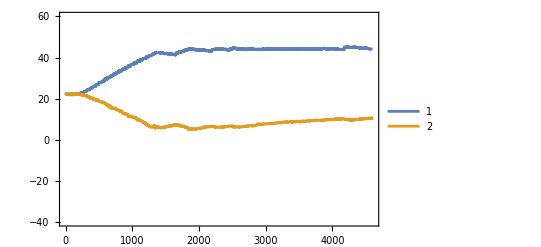

```mathematica
ListPlot[{c1,c2},Joined->True,PlotRange->{-40,60},Axes->False,Frame->True,PlotLegends->Automatic]
```

```mathematica
a[[Length[a],3]]
```

44.1875

```mathematica
a[[Length[a],4]]
```

10.625

```mathematica
Length[a]
```

4601

```mathematica
%/5.
```

920.2

```mathematica
aa=Table[a[[i,4]],{i,10000,Length[a]}];
```

```mathematica
amx=Max[aa]
```

-∞

```mathematica
Do[If[aa[[i]]==amx,Print[i];indx=i],{i,Length[aa]}]
```

```mathematica
aa[[indx]]==amx
```

Part::pkspec1: The expression indx cannot be used as a part specification.

{}⟦indx⟧==-∞

```mathematica
(Sum[aa[[i]],{i,Length[aa]}]-amx)/(Length[aa]-1)
```

-∞

```mathematica
bb=Table[a[[i,3]],{i,10000,Length[a]}];
```

```mathematica
(Sum[bb[[i]],{i,Length[bb]}])/(Length[bb])
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate